Mohr's Circle

Input stress tensor (generalized plane stress)

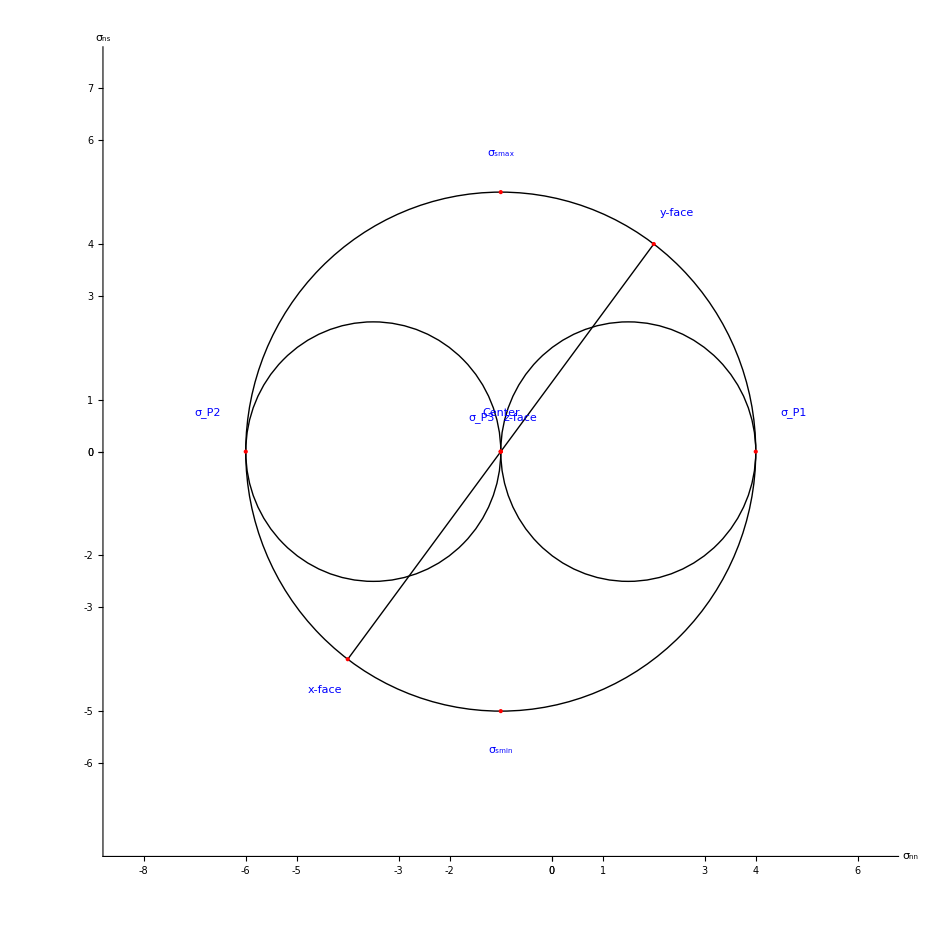

{(σ =  | (-4. | 4. | 0.
4. | 2. | 0.
0. | 0. | -1.)),(x-face | {-4,-4}
y-face | {2,4}
z-face | {-1,0}
Center | {-1,0}
σ_P1 | {4,0}
σ_P2 | {-6,0}
σ_P3 | {-1,0}
σ_smax | {-1,5}
σ_smin | {-1,-5}),(x-face | {-4.,-4.}
y-face | {2.,4.}
z-face | {-1.,0.}
Center | {-1.,0.}
σ_P1 | {4.,0.}
σ_P2 | {-6.,0.}
σ_P3 | {-1.,0.}
σ_smax | {-1.,5.}
σ_smin | {-1.,-5.})}

{(σ =  | (9. | 6. | 0.
6. | -7. | 0.
0. | 0. | -13.)),(x-face | {9.,-6.}
y-face | {-7.,6.}
z-face | {-13.,0}
Center | {1.,0}
σ_P1 | {11.,0}
σ_P2 | {-9.,0}
σ_P3 | {-13.,0}
σ_smax | {-1.,12.}
σ_smin | {-1.,-12.}),(x-face | {9.,-6.}
y-face | {-7.,6.}
z-face | {-13.,0.}
Center | {1.,0.}
σ_P1 | {11.,0.}
σ_P2 | {-9.,0.}
σ_P3 | {-13.,0.}
σ_smax | {-1.,12.}
σ_smin | {-1.,-12.})}

```mathematica
ClearAll["Global`*"]
sigma={{7,4,0},{4,2,0},{0,0,-1}};
sigma={{-4,4,0},{4,2,0},{0,0,-1}};
(*sigma={{4,5,0},{5,-3,0},{0,0,8}};
sigma={{-40,0,0},{0,-10,30},{0,30,-20}};
sigma={{-40,0,30},{0,-10,0},{30,0,-20}};
sigma=N[{{-40,0,30},{0,-10,0},{30,0,-20}}];
sigma={{4,5,0},{5,-3,0},{0,0,8}};
sigma=N[{{-40,0,30},{0,-10,0},{30,0,-20}}];
sigma=N[{{-4,0,6},{0,12,0},{6,0,8}}];
(*sigma=N[{{4,5,0},{5,-2,0},{0,0,8}}];*)
(*sigma=N[{{9,6,0},{6,-7,0},{0,0,-13}}];*)*)

If[sigma[[1,2]]≠0,plane="xy"];
If[sigma[[1,3]]≠0,plane="xz"];
If[sigma[[2,3]]≠0,plane="yz"];

If[plane=="xy",{givenpoints={{sigma[[1,1]],-sigma[[1,2]]},{sigma[[2,2]],sigma[[1,2]]},{sigma[[3,3]],0}},center=(sigma[[1,1]]+sigma[[2,2]])/2,radius=Sqrt[((sigma[[1,1]]-sigma[[2,2]])/2)^2+sigma[[1,2]]^2]}];
If[plane=="xz",{givenpoints={{sigma[[1,1]],sigma[[1,3]]},{sigma[[2,2]],0},{sigma[[3,3]],-sigma[[1,3]]}},center=(sigma[[1,1]]+sigma[[3,3]])/2,radius=Sqrt[((sigma[[1,1]]-sigma[[3,3]])/2)^2+sigma[[1,3]]^2]}];
If[plane=="yz",{givenpoints={{sigma[[1,1]],0},{sigma[[2,2]],-sigma[[2,3]]},{sigma[[3,3]],sigma[[2,3]]}},center=(sigma[[2,2]]+sigma[[3,3]])/2,radius=Sqrt[((sigma[[2,2]]-sigma[[3,3]])/2)^2+sigma[[2,3]]^2]}];

If[plane=="xy",
{sigmaP1=center+radius,
sigmaP2=center-radius,
sigmaP3=sigma[[3,3]]}];
If[plane=="xz",
{sigmaP1=center+radius,
sigmaP2=sigma[[2,2]],
sigmaP3=center-radius}];
If[plane=="yz",
{sigmaP1=sigma[[1,1]],
sigmaP2=center+radius,
sigmaP3=center-radius}];

displaycenter={(Min[sigmaP1,sigmaP2,sigmaP3]+Max[sigmaP1,sigmaP2,sigmaP3])/2,0};
displaydim=1.5*.5*{Max[sigmaP1,sigmaP2,sigmaP3]-Min[sigmaP1,sigmaP2,sigmaP3],2*radius};
displayrange={{displaycenter[[1]]-displaydim[[1]],displaycenter[[1]]+displaydim[[1]]},{displaycenter[[2]]-displaydim[[2]],displaycenter[[2]]+displaydim[[2]]}};
displayelement=.1*((displaydim[[1]]+displaydim[[2]])/2);

numticks=10;
tickspacingx=Abs[ displayrange[[1,2]]-displayrange[[1,1]] ]/numticks;
tickspacingy=Abs[ displayrange[[2,2]]-displayrange[[2,1]] ]/numticks;

If[plane=="xy",
circledata={{center,0,radius},{(sigmaP2+sigmaP3)/2,0,Abs[sigmaP2-sigmaP3]/2},{(sigmaP1+sigmaP3)/2,0,Abs[sigmaP1-sigmaP3]/2}}];
If[plane=="xz",
circledata={{center,0,radius},{(sigmaP1+sigmaP2)/2,0,Abs[sigmaP1-sigmaP2]/2},{(sigmaP2+sigmaP3)/2,0,Abs[sigmaP2-sigmaP3]/2}}];
If[plane=="yz",
circledata={{center,0,radius},{(sigmaP1+sigmaP2)/2,0,Abs[sigmaP1-sigmaP2]/2},{(sigmaP1+sigmaP3)/2,0,Abs[sigmaP1-sigmaP3]/2}}];

largestcircle=1;
rowmax=Dimensions[circledata,1];
For[row=1,row≤rowmax[[1]],row++,
{
If[circledata[[row,3]]>circledata[[largestcircle,3]],largestcircle=row]
}
]

circle1:=Graphics[{Circle[{circledata[[1,1]],circledata[[1,2]]},circledata[[1,3]]],
Circle[{circledata[[2,1]],circledata[[2,2]]},circledata[[2,3]]],
Circle[{circledata[[3,1]],circledata[[3,2]]},circledata[[3,3]]]},
Axes->True,
AxesLabel->{Subscript[σ,nn],Subscript[σ,ns]},
LabelStyle->Directive[Large,Bold],
Ticks->{ Floor[ Table[tickspacingx*Floor[.5*n]*(-1)^Floor[1.5*n],{n,0,Ceiling[(2*Max[Abs[ displayrange[[1]] ]]+1)/tickspacingx]}] ], Floor[ Table[tickspacingy*Floor[.5*n]*(-1)^Floor[1.5*n],{n,0,Ceiling[(2*Max[Abs[ displayrange[[2]] ]]+1)/tickspacingy]}] ] },
TicksStyle->Directive[Small,Italic],
PlotRange->displayrange,
AspectRatio->1];

If[plane=="xy",
line1:=Graphics[Line[ {givenpoints[[1]],givenpoints[[2]]} ]] ];
If[plane=="xz",
line1:=Graphics[Line[ {givenpoints[[1]],givenpoints[[3]]} ]] ];
If[plane=="yz",
line1:=Graphics[Line[ {givenpoints[[2]],givenpoints[[3]]} ]] ];

pointsdata={ givenpoints[[1]],givenpoints[[2]],givenpoints[[3]],{center,0}, {sigmaP1,0}, {sigmaP2,0}, {sigmaP3,0},{circledata[[largestcircle,1]],circledata[[largestcircle,3]]},{circledata[[largestcircle,1]],-circledata[[largestcircle,3]]} };

points1:=Graphics[
{PointSize[Large],Red,Point[pointsdata]}
];

r1=N[ pointsdata-ConstantArray[displaycenter,Dimensions[pointsdata,1]] ];
dim=Dimensions[r1,1];
r1norm=N[ Table[ {Norm[ r1[[i]] ],Norm[  r1[[i]] ]},{ i,dim[[1]] } ] ];

r2=ConstantArray[{0,0},dim[[1]]];
For[row=1,row≤dim[[1]],row++,
If[ r1norm[[row,1]]≠0,r2[[row]]=displayelement*r1[[row]]/r1norm[[row]] ]
]

annotationdata=ConstantArray[displaycenter,Dimensions[pointsdata,1]]+r1+r2;

dim=Dimensions[annotationdata,1];
For[row=1,row≤dim[[1]],row++,{
If[ Abs[annotationdata[[row,1]] ]<displayelement,
{ annotationdata[[row,1]]=displayelement*(2*Ceiling[(Sign[annotationdata[[row,1]]]+1)/2]-1),
r2[[row]]=annotationdata[[row]]-pointsdata[[row]] }
],
If[ Abs[annotationdata[[row,2]] ]<displayelement,
{ annotationdata[[row,2]]=displayelement*(2*Ceiling[(Sign[annotationdata[[row,2]]]+1)/2]-1),
r2[[row]]=annotationdata[[row]]-pointsdata[[row]] }
]
}];

duplicates={};
temparray=annotationdata;
dim=Dimensions[temparray,1];
For[row1=1,row1≤dim[[1]]-1,row1++,
{temp={row1},
For[row2=row1+1,row2≤dim[[1]],row2++,
If[EuclideanDistance[ temparray[[row2]],temparray[[row1]] ]≤displayelement&&temparray[[row2]]≠{},
{temp=Append[temp,row2],temparray[[row2]]={}}
]
],
If[ Length[temp]>1,duplicates=Append[duplicates,temp] ]}
]

rmatrix[theta_]={{Cos[theta],Sin[theta]},{-Sin[theta],Cos[theta]}};
dim=Dimensions[duplicates,1];
For[row=1,row≤dim[[1]],row++,
{numcollisions=Length[ duplicates[[row]] ],
If[ numcollisions>1,
{spread=(Pi/6)*(Range[0,numcollisions-1]-N[ Median[ Range[ 0, numcollisions-1 ] ] ]),
For[col=1,col≤Length[ duplicates[[row]] ],col++,
r2[[ duplicates[[row,col]] ]]=r2[[ duplicates[[row,col]] ]].rmatrix[ spread[[col]] ]
]}
]}
]

annotationdata=ConstantArray[displaycenter,Dimensions[pointsdata,1]]+r1+r2;

annotation1:=Graphics[Text[Style["x-face",Larger,Blue],annotationdata[[1]] ]];
annotation2:=Graphics[Text[Style["y-face",Larger,Blue],annotationdata[[2]] ]];
annotation3:=Graphics[Text[Style["z-face",Larger,Blue],annotationdata[[3]] ]];
annotation4:=Graphics[Text[Style["Center",Larger,Blue],annotationdata[[4]] ]];
annotation5:=Graphics[Text[Style[Subscript[σ,P1],Larger,Blue],annotationdata[[5]] ]];
annotation6:=Graphics[Text[Style[Subscript[σ,P2],Larger,Blue],annotationdata[[6]] ]];
annotation7:=Graphics[Text[Style[Subscript[σ,P3],Larger,Blue],annotationdata[[7]] ]];
annotation8:=Graphics[Text[Style[Subscript[σ,smax],Larger,Blue],annotationdata[[8]] ]];
annotation9:=Graphics[Text[Style[Subscript[σ,smin],Larger,Blue],annotationdata[[9]] ]];

f1[x_]=.466*x-7;
f2[x_]=-.466*x+7;
region1:=Plot[{f1[x],f2[x]},{x,displayrange[[1,1]],displayrange[[1,2]]}];


Show[circle1,line1,points1,annotation1,annotation2,annotation3,annotation4,annotation5,annotation6,annotation7,annotation8,annotation9]

{{{"σ = ",N[sigma]//MatrixForm}}//MatrixForm,
{{"x-face",pointsdata[[1]]},
{"y-face",pointsdata[[2]]},
{"z-face",pointsdata[[3]]},
{"Center",pointsdata[[4]]},
{Subscript[σ,P1],pointsdata[[5]]},
{Subscript[σ,P2],pointsdata[[6]]},
{Subscript[σ,P3],pointsdata[[7]]},
{Subscript[σ,smax],pointsdata[[8]]},
{Subscript[σ,smin],pointsdata[[9]]}
}//MatrixForm,N[{{"x-face",pointsdata[[1]]},
{"y-face",pointsdata[[2]]},
{"z-face",pointsdata[[3]]},
{"Center",pointsdata[[4]]},
{Subscript[σ,P1],pointsdata[[5]]},
{Subscript[σ,P2],pointsdata[[6]]},
{Subscript[σ,P3],pointsdata[[7]]},
{Subscript[σ,smax],pointsdata[[8]]},
{Subscript[σ,smin],pointsdata[[9]]}
}]//MatrixForm}
```